```mathematica
t = 5;
a = With[{t=5},t/;1>0]
```

5/;1>0

```mathematica
b:>a
```

5/;1>0:>a

```mathematica
StringTake[ResourceData["Lorem Ipsum"], 100]
```

Lorem ipsum dolor sit amet, consectetuer adipiscing elit. Integer nunc augue, feugiat non, egestas u

```mathematica
WordCloud@DeleteStopwords@TextWords@WikipediaData["Moldova"]
```

```mathematica
maxLength=Max@StringLength@WordList[]
```

23

```mathematica
Select[WordList[],StringLength[#]==maxLength&]
```

{electroencephalographic}

```mathematica
SortBy[WordList[],-StringLength[#]&]
```

{electroencephalographic,electroencephalograph,buckminsterfullerene,compartmentalization,counterrevolutionary,electroencephalogram,internationalization,magnetohydrodynamics,uncharacteristically,counterintelligence,39156,TV,um,up,us,we,xi,ya,ye,a,I}
 |  |  |  |

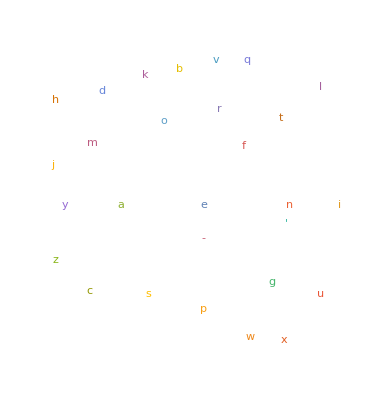

```mathematica
WordCloud@Characters@StringJoin@WordList[]
```

```mathematica
n = 20;
Hue /@Table[i/n,{i,0,n - 1}]
```

{Hue[0],Hue[Rational[1, 20]],Hue[Rational[1, 10]],Hue[Rational[3, 20]],Hue[Rational[1, 5]],Hue[Rational[1, 4]],Hue[Rational[3, 10]],Hue[Rational[7, 20]],Hue[Rational[2, 5]],Hue[Rational[9, 20]],Hue[Rational[1, 2]],Hue[Rational[11, 20]],Hue[Rational[3, 5]],Hue[Rational[13, 20]],Hue[Rational[7, 10]],Hue[Rational[3, 4]],Hue[Rational[4, 5]],Hue[Rational[17, 20]],Hue[Rational[9, 10]],Hue[Rational[19, 20]]}

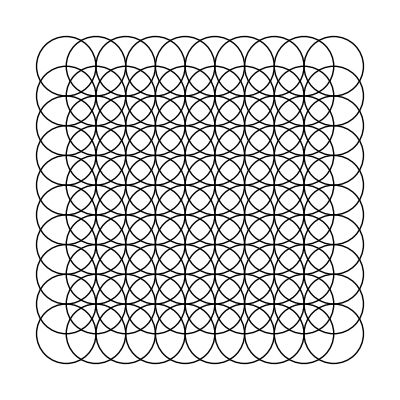

```mathematica
Map[Circle[#,1]&,Flatten[Table[{i,j},{i,0,9},{j,0,9}],1]]//Graphics
```

```mathematica
r=10;
Table[Style[Sphere[{x,y,z},0.5],RGBColor[x/10,y/10,z/10]],{x,0,r-1},{y,0,r-1},{z,0,r-1}]//Graphics3D
```

-Graphics3D-

```mathematica
|
```